1600 bosons

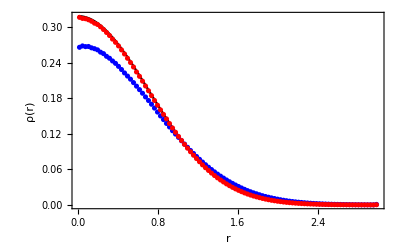

```mathematica
density1600={{0.015,0.265784},{0.045,0.268056},{0.075,0.266902},{0.105,0.267109},{0.135,0.264869},{0.165,0.263394},{0.195,0.261454},{0.225,0.257578},{0.255,0.255075},{0.285,0.250573},{0.315,0.247307},{0.345,0.242735},{0.375,0.238685},{0.405,0.233628},{0.435,0.228288},{0.465,0.222527},{0.495,0.217271},{0.525,0.211993},{0.555,0.206226},{0.585,0.200249},{0.615,0.19438},{0.645,0.188309},{0.675,0.18208},{0.705,0.176045},{0.735,0.169775},{0.765,0.163314},{0.795,0.156567},{0.825,0.150045},{0.855,0.143935},{0.885,0.1374},{0.915,0.131434},{0.945,0.125114},{0.975,0.119477},{1.005,0.113927},{1.035,0.108244},{1.065,0.102629},{1.095,0.097164},{1.125,0.091809},{1.155,0.086741},{1.185,0.081712},{1.215,0.076915},{1.245,0.0723},{1.275,0.067832},{1.305,0.06361},{1.335,0.05964},{1.365,0.05573},{1.395,0.052003},{1.425,0.048565},{1.455,0.045286},{1.485,0.042097},{1.515,0.039074},{1.545,0.036306},{1.575,0.033579},{1.605,0.031091},{1.635,0.028619},{1.665,0.026315},{1.695,0.024133},{1.725,0.022216},{1.755,0.020379},{1.785,0.018775},{1.815,0.017137},{1.845,0.015537},{1.875,0.014187},{1.905,0.012984},{1.935,0.011835},{1.965,0.01076},{1.995,0.009715},{2.025,0.008743},{2.055,0.007874},{2.085,0.007096},{2.115,0.006352},{2.145,0.005723},{2.175,0.005136},{2.205,0.004616},{2.235,0.004116},{2.265,0.003674},{2.295,0.003258},{2.325,0.002876},{2.355,0.002529},{2.385,0.002247},{2.415,0.001987},{2.445,0.001745},{2.475,0.001534},{2.505,0.001353},{2.535,0.001172},{2.565,0.001025},{2.595,0.000907},{2.625,0.000793},{2.655,0.000698},{2.685,0.000599},{2.715,0.000514},{2.745,0.000442},{2.775,0.000389},{2.805,0.000336},{2.835,0.00028},{2.865,0.000246},{2.895,0.000208},{2.925,0.000181},{2.955,0.000155},{2.985,0.000847}};(*5000+5000 MD steps*)
density1600B={{0.015,0.316252},{0.045,0.314452},{0.075,0.313919},{0.105,0.312143},{0.135,0.309691},{0.165,0.306397},{0.195,0.304247},{0.225,0.300308},{0.255,0.29575},{0.285,0.290771},{0.315,0.285632},{0.345,0.279592},{0.375,0.274134},{0.405,0.268108},{0.435,0.261405},{0.465,0.25451},{0.495,0.247271},{0.525,0.240107},{0.555,0.232548},{0.585,0.224226},{0.615,0.216806},{0.645,0.208731},{0.675,0.200547},{0.705,0.192476},{0.735,0.184286},{0.765,0.176147},{0.795,0.168091},{0.825,0.16022},{0.855,0.152591},{0.885,0.145085},{0.915,0.13723},{0.945,0.129758},{0.975,0.122525},{1.005,0.115452},{1.035,0.1087},{1.065,0.102057},{1.095,0.095715},{1.125,0.089675},{1.155,0.083834},{1.185,0.078187},{1.215,0.072814},{1.245,0.067573},{1.275,0.062734},{1.305,0.058152},{1.335,0.053733},{1.365,0.049589},{1.395,0.045683},{1.425,0.04209},{1.455,0.038727},{1.485,0.035438},{1.515,0.032459},{1.545,0.029654},{1.575,0.027074},{1.605,0.024638},{1.635,0.022413},{1.665,0.020308},{1.695,0.018383},{1.725,0.016657},{1.755,0.015049},{1.785,0.013637},{1.815,0.01229},{1.845,0.010992},{1.875,0.009868},{1.905,0.008815},{1.935,0.00787},{1.965,0.007051},{1.995,0.006286},{2.025,0.005606},{2.055,0.00496},{2.085,0.004377},{2.115,0.003873},{2.145,0.003433},{2.175,0.003019},{2.205,0.002659},{2.235,0.00235},{2.265,0.002047},{2.295,0.001798},{2.325,0.001585},{2.355,0.001375},{2.385,0.001189},{2.415,0.001022},{2.445,0.000902},{2.475,0.000772},{2.505,0.00067},{2.535,0.000577},{2.565,0.000489},{2.595,0.000428},{2.625,0.000381},{2.655,0.000326},{2.685,0.000277},{2.715,0.000238},{2.745,0.000201},{2.775,0.000169},{2.805,0.000142},{2.835,0.00012},{2.865,0.000101},{2.895,0.000084},{2.925,0.000077},{2.955,0.000063},{2.985,0.000348}};(*10000+10000 MD steps*)
Show[ Plot[ Exp[-x^2]/Pi,{x,0,3},PlotStyle->Black],ListPlot[{density1600,density1600B},PlotStyle->{Blue,Red}],Frame->True,FrameLabel->{{HoldForm["ρ(r)"],None},{HoldForm["r"],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0]}]
```

5000 bosons

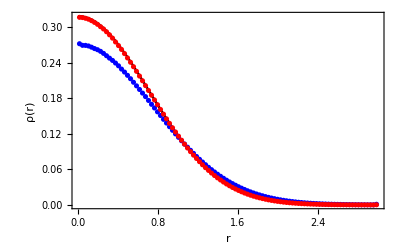

```mathematica
density5000={{0.015,0.271753},{0.045,0.269078},{0.075,0.26896},{0.105,0.267988},{0.135,0.265961},{0.165,0.263629},{0.195,0.261691},{0.225,0.258968},{0.255,0.255508},{0.285,0.251542},{0.315,0.247482},{0.345,0.24364},{0.375,0.239224},{0.405,0.234548},{0.435,0.229041},{0.465,0.224009},{0.495,0.218481},{0.525,0.212787},{0.555,0.206808},{0.585,0.200773},{0.615,0.194685},{0.645,0.188558},{0.675,0.182635},{0.705,0.17615},{0.735,0.169629},{0.765,0.163482},{0.795,0.156919},{0.825,0.150745},{0.855,0.144333},{0.885,0.138095},{0.915,0.131882},{0.945,0.125863},{0.975,0.119766},{1.005,0.113989},{1.035,0.108284},{1.065,0.102685},{1.095,0.097375},{1.125,0.092117},{1.155,0.086931},{1.185,0.081689},{1.215,0.076925},{1.245,0.07235},{1.275,0.067866},{1.305,0.063459},{1.335,0.059469},{1.365,0.055575},{1.395,0.051829},{1.425,0.048307},{1.455,0.044954},{1.485,0.041749},{1.515,0.0387},{1.545,0.035949},{1.575,0.033244},{1.605,0.030684},{1.635,0.028306},{1.665,0.026058},{1.695,0.023908},{1.725,0.021979},{1.755,0.020151},{1.785,0.018448},{1.815,0.016865},{1.845,0.015417},{1.875,0.014016},{1.905,0.012742},{1.935,0.011584},{1.965,0.010519},{1.995,0.009502},{2.025,0.00858},{2.055,0.007759},{2.085,0.006992},{2.115,0.006305},{2.145,0.005651},{2.175,0.005061},{2.205,0.004507},{2.235,0.004017},{2.265,0.003587},{2.295,0.003209},{2.325,0.002857},{2.355,0.002532},{2.385,0.002268},{2.415,0.001987},{2.445,0.001758},{2.475,0.001567},{2.505,0.001373},{2.535,0.001215},{2.565,0.001069},{2.595,0.000945},{2.625,0.000824},{2.655,0.000717},{2.685,0.000629},{2.715,0.000554},{2.745,0.000483},{2.775,0.000417},{2.805,0.000363},{2.835,0.000309},{2.865,0.000271},{2.895,0.00023},{2.925,0.000199},{2.955,0.000177},{2.985,0.00108}};
density5000B={{0.015,0.316273},{0.045,0.315913},{0.075,0.314689},{0.105,0.313125},{0.135,0.310666},{0.165,0.30775},{0.195,0.304478},{0.225,0.300484},{0.255,0.296633},{0.285,0.291946},{0.315,0.286773},{0.345,0.281197},{0.375,0.274749},{0.405,0.268597},{0.435,0.262169},{0.465,0.255173},{0.495,0.24782},{0.525,0.240558},{0.555,0.23303},{0.585,0.225269},{0.615,0.217271},{0.645,0.209358},{0.675,0.201158},{0.705,0.192983},{0.735,0.185025},{0.765,0.176994},{0.795,0.168975},{0.825,0.160978},{0.855,0.153029},{0.885,0.145157},{0.915,0.137498},{0.945,0.130092},{0.975,0.122946},{1.005,0.115921},{1.035,0.109108},{1.065,0.102455},{1.095,0.096009},{1.125,0.089862},{1.155,0.083989},{1.185,0.078339},{1.215,0.07293},{1.245,0.067715},{1.275,0.062818},{1.305,0.058213},{1.335,0.053787},{1.365,0.049609},{1.395,0.045662},{1.425,0.042068},{1.455,0.038599},{1.485,0.035322},{1.515,0.032295},{1.545,0.02947},{1.575,0.026891},{1.605,0.024473},{1.635,0.022229},{1.665,0.020121},{1.695,0.018172},{1.725,0.016417},{1.755,0.01478},{1.785,0.013303},{1.815,0.011968},{1.845,0.010741},{1.875,0.009615},{1.905,0.008564},{1.935,0.007665},{1.965,0.006806},{1.995,0.006057},{2.025,0.005391},{2.055,0.004765},{2.085,0.004196},{2.115,0.003692},{2.145,0.003266},{2.175,0.002885},{2.205,0.002522},{2.235,0.002219},{2.265,0.001942},{2.295,0.001708},{2.325,0.001486},{2.355,0.001292},{2.385,0.001122},{2.415,0.000974},{2.445,0.000851},{2.475,0.000728},{2.505,0.000624},{2.535,0.000541},{2.565,0.000462},{2.595,0.000393},{2.625,0.000336},{2.655,0.00029},{2.685,0.000248},{2.715,0.000209},{2.745,0.00018},{2.775,0.00015},{2.805,0.000127},{2.835,0.000105},{2.865,0.000088},{2.895,0.000076},{2.925,0.000064},{2.955,0.000055},{2.985,0.00027}};
Show[ Plot[ Exp[-x^2]/Pi,{x,0,3},PlotStyle->Black],ListPlot[{density5000,density5000B},PlotStyle->{Blue,Red}],Frame->True,FrameLabel->{{HoldForm["ρ(r)"],None},{HoldForm["r"],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0]}]
```

10000 bosons

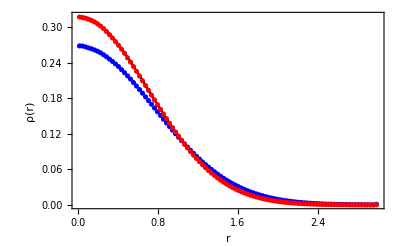

```mathematica
density10000={{0.015,0.26808},{0.045,0.267928},{0.075,0.266511},{0.105,0.264802},{0.135,0.263297},{0.165,0.261284},{0.195,0.259164},{0.225,0.256474},{0.255,0.253294},{0.285,0.249793},{0.315,0.245821},{0.345,0.241874},{0.375,0.237648},{0.405,0.233213},{0.435,0.228084},{0.465,0.223},{0.495,0.217548},{0.525,0.212154},{0.555,0.206293},{0.585,0.200469},{0.615,0.194559},{0.645,0.188435},{0.675,0.18225},{0.705,0.175901},{0.735,0.169672},{0.765,0.163335},{0.795,0.157049},{0.825,0.150824},{0.855,0.144397},{0.885,0.138224},{0.915,0.132122},{0.945,0.126067},{0.975,0.120122},{1.005,0.114173},{1.035,0.108486},{1.065,0.102927},{1.095,0.09748},{1.125,0.092162},{1.155,0.08703},{1.185,0.082087},{1.215,0.077262},{1.245,0.072534},{1.275,0.068092},{1.305,0.063831},{1.335,0.059753},{1.365,0.05583},{1.395,0.052016},{1.425,0.048435},{1.455,0.045048},{1.485,0.041913},{1.515,0.038843},{1.545,0.035972},{1.575,0.033298},{1.605,0.030781},{1.635,0.028414},{1.665,0.026068},{1.695,0.023998},{1.725,0.022012},{1.755,0.020206},{1.785,0.018484},{1.815,0.016925},{1.845,0.015443},{1.875,0.014077},{1.905,0.012819},{1.935,0.01164},{1.965,0.010543},{1.995,0.009534},{2.025,0.008641},{2.055,0.007807},{2.085,0.007027},{2.115,0.006333},{2.145,0.005682},{2.175,0.005101},{2.205,0.004552},{2.235,0.004071},{2.265,0.003637},{2.295,0.003247},{2.325,0.002889},{2.355,0.002568},{2.385,0.002278},{2.415,0.002012},{2.445,0.001778},{2.475,0.00157},{2.505,0.00138},{2.535,0.001215},{2.565,0.001075},{2.595,0.000943},{2.625,0.000826},{2.655,0.00073},{2.685,0.000637},{2.715,0.000555},{2.745,0.000484},{2.775,0.000415},{2.805,0.000362},{2.835,0.000312},{2.865,0.000271},{2.895,0.000234},{2.925,0.000205},{2.955,0.000179},{2.985,0.001102}};
density10000B={{0.015,0.316765},{0.045,0.315604},{0.075,0.314803},{0.105,0.31298},{0.135,0.311063},{0.165,0.308452},{0.195,0.305274},{0.225,0.301558},{0.255,0.297422},{0.285,0.292333},{0.315,0.286962},{0.345,0.281291},{0.375,0.275321},{0.405,0.269103},{0.435,0.262613},{0.465,0.255612},{0.495,0.248166},{0.525,0.240826},{0.555,0.233218},{0.585,0.225259},{0.615,0.21731},{0.645,0.209409},{0.675,0.201284},{0.705,0.193151},{0.735,0.185122},{0.765,0.176976},{0.795,0.168969},{0.825,0.161238},{0.855,0.153218},{0.885,0.145457},{0.915,0.137773},{0.945,0.130381},{0.975,0.122994},{1.005,0.115972},{1.035,0.109049},{1.065,0.102443},{1.095,0.096054},{1.125,0.089851},{1.155,0.083945},{1.185,0.078238},{1.215,0.072873},{1.245,0.067643},{1.275,0.062709},{1.305,0.058028},{1.335,0.053644},{1.365,0.049481},{1.395,0.045563},{1.425,0.041889},{1.455,0.038399},{1.485,0.035182},{1.515,0.032178},{1.545,0.029377},{1.575,0.026762},{1.605,0.024344},{1.635,0.022099},{1.665,0.020048},{1.695,0.018134},{1.725,0.016375},{1.755,0.014769},{1.785,0.01328},{1.815,0.011936},{1.845,0.01072},{1.875,0.009591},{1.905,0.008593},{1.935,0.007643},{1.965,0.00681},{1.995,0.006056},{2.025,0.005368},{2.055,0.00474},{2.085,0.004193},{2.115,0.003702},{2.145,0.003267},{2.175,0.002872},{2.205,0.002525},{2.235,0.002211},{2.265,0.001935},{2.295,0.001691},{2.325,0.001473},{2.355,0.001278},{2.385,0.001114},{2.415,0.000967},{2.445,0.000836},{2.475,0.000719},{2.505,0.000623},{2.535,0.000537},{2.565,0.000461},{2.595,0.000395},{2.625,0.00034},{2.655,0.000287},{2.685,0.000244},{2.715,0.000206},{2.745,0.000175},{2.775,0.00015},{2.805,0.000129},{2.835,0.000107},{2.865,0.00009},{2.895,0.000076},{2.925,0.000063},{2.955,0.000053},{2.985,0.000269}};
Show[ Plot[ Exp[-x^2]/Pi,{x,0,3},PlotStyle->Black],ListPlot[{density10000,density10000B},PlotStyle->{Blue,Red}],Frame->True,FrameLabel->{{HoldForm["ρ(r)"],None},{HoldForm["r"],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0]}]
```

20000 bosons

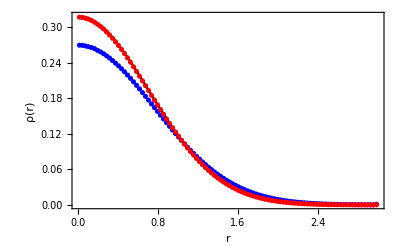

```mathematica
density20000B={{0.015,0.316518},{0.045,0.315947},{0.075,0.314675},{0.105,0.31326},{0.135,0.310874},{0.165,0.30802},{0.195,0.304576},{0.225,0.300913},{0.255,0.296654},{0.285,0.291742},{0.315,0.286563},{0.345,0.280982},{0.375,0.27498},{0.405,0.268751},{0.435,0.262124},{0.465,0.255167},{0.495,0.248072},{0.525,0.240558},{0.555,0.232904},{0.585,0.225049},{0.615,0.217146},{0.645,0.209087},{0.675,0.201033},{0.705,0.192945},{0.735,0.184774},{0.765,0.176698},{0.795,0.168699},{0.825,0.160851},{0.855,0.152953},{0.885,0.145129},{0.915,0.137589},{0.945,0.130141},{0.975,0.123001},{1.005,0.115979},{1.035,0.109094},{1.065,0.102413},{1.095,0.096039},{1.125,0.089951},{1.155,0.0841},{1.185,0.078408},{1.215,0.072971},{1.245,0.067813},{1.275,0.062882},{1.305,0.05823},{1.335,0.053859},{1.365,0.049678},{1.395,0.045763},{1.425,0.042076},{1.455,0.038626},{1.485,0.035371},{1.515,0.032359},{1.545,0.029532},{1.575,0.026901},{1.605,0.024471},{1.635,0.022203},{1.665,0.020131},{1.695,0.018205},{1.725,0.016452},{1.755,0.014837},{1.785,0.013352},{1.815,0.011981},{1.845,0.010728},{1.875,0.009604},{1.905,0.008588},{1.935,0.007649},{1.965,0.006805},{1.995,0.006043},{2.025,0.005361},{2.055,0.004751},{2.085,0.004195},{2.115,0.003702},{2.145,0.00326},{2.175,0.002864},{2.205,0.002512},{2.235,0.002205},{2.265,0.001926},{2.295,0.001679},{2.325,0.001466},{2.355,0.001274},{2.385,0.001106},{2.415,0.000959},{2.445,0.000832},{2.475,0.000717},{2.505,0.000619},{2.535,0.000532},{2.565,0.000455},{2.595,0.000392},{2.625,0.000335},{2.655,0.000287},{2.685,0.000243},{2.715,0.000208},{2.745,0.000177},{2.775,0.00015},{2.805,0.000128},{2.835,0.000108},{2.865,0.000091},{2.895,0.000077},{2.925,0.000065},{2.955,0.000054},{2.985,0.000276}};
Show[ Plot[ Exp[-x^2]/Pi,{x,0,3},PlotStyle->Black],ListPlot[{density20000A,density20000B},PlotStyle->{Blue,Red}],Frame->True,FrameLabel->{{HoldForm["ρ(r)"],None},{HoldForm["r"],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0]}]
```